```mathematica
Z0[L_,β_]:=1/2 (2 Sinh[2β])^(L^2/2) 
c[l_,L_,β_]:=Cosh[2β]Coth[2β]-Cos[Pi l/L]
Z1[L_,β_]:=2^L Product[ChebyshevT[L/2, c[2 r+1,L,β]],{r,0,L-1}]
Z2[L_,β_]:=2^L Product[ChebyshevU[L/2-1, c[2 r+1,L,β]],{r,0,L-1}] Product[(c[2 r+1,L,β]^2-1),{r,0,L/2-1}]
Z3[L_,β_]:=2^L Product[ChebyshevT[L/2, c[2 r,L,β]],{r,0,L-1}]
Z4[L_,β_]:=2^L Product[ChebyshevU[L/2-1, c[2 r,L,β]],{r,0,L-1}]Product[(c[2 r,L,β]^2-1),{r,1,L/2-1}](Cosh[2β]^2 - Coth[2β]^2)
Z[L_,β_]:=Z0[L,β](Z1[L,β]+Z2[L,β]+Z3[L,β]+Z4[L,β])
```

```mathematica
entropy[logz_]:=logz - β D[logz,β]
```

```mathematica
energy[logz_]:=-D[logz,β]
```

```mathematica
LogZ20 =Log[Z[20,β]];
S20= entropy[LogZ20];
energy20=energy[LogZ20];
varenergy20=energy[energy20];
```

```mathematica
s20[β_]=S20/20^2/Log[2];
en20[β_]=energy20/20^2;
varen20[β_]=varenergy20/20^2;
f20[β_]=-1/β LogZ20/20^2;
```

```mathematica
Ts=Table[T,{T,1.0,4.0,0.1}]
```

{1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.}

```mathematica
xT[l_]:=Transpose[{Ts, l}]
```

```mathematica
energies20 = Table[en20[1/T],{T,1.0,4.0,0.1}];
```

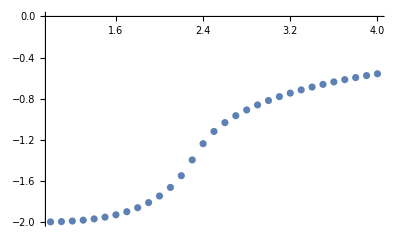

```mathematica
ListPlot[xT[energies20]]
```

```mathematica
Export["energies20.txt", energies20]
```

energies20.txt

```mathematica
varenergies20 = Table[varen20[1/T],{T,1.0,4.0,0.1}];
```

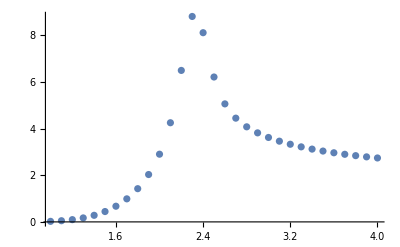

```mathematica
ListPlot[xT[varenergies20]]
```

```mathematica
Export["varenergies20.txt", varenergies20]
```

varenergies20.txt

```mathematica
entropies20 = Table[s20[1/T],{T,1.0,4.0,0.1}];
```

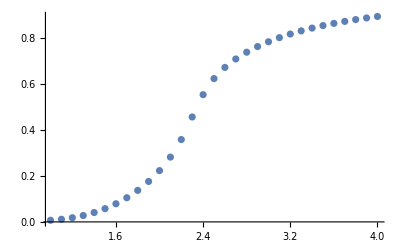

```mathematica
ListPlot[xT[entropies20]]
```

```mathematica
Export["entropies20.txt", entropies20]
```

entropies20.txt

```mathematica
freeenergies20 = Table[f20[1/T],{T,1.0,4.0,0.1}];
```

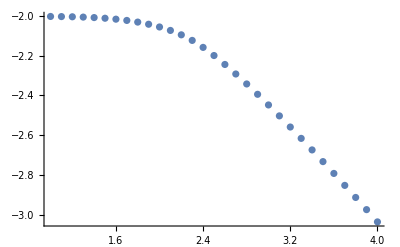

```mathematica
ListPlot[xT[freeenergies20]]
```

```mathematica
Export["freeenergies20.txt", freeenergies20]
```

freeenergies20.txt

```mathematica
Tc=2.2691853;
```

```mathematica
en20[1/Tc]
```

-1.44531

```mathematica
varen20[1/Tc]
```

8.2962

```mathematica
s20[1/Tc]
```

0.424682

```mathematica
f20[1/Tc]
```

-2.11328